```mathematica
(* Student Name *)
(* Jun 21, 2017 *)
(* MITES Physics III: Intro to Oscillations and Waves *)
(* Numerical Solution to Differential Equations *)

(* Correct the Code Below So that it produces Oscillatory Rather than Exponential Motion *)
```

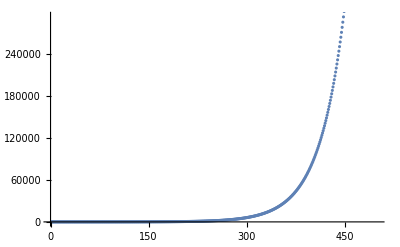

```mathematica
x0 = 5.0; (* Defines the initial position of the mass *) 

xdot0 = 0.0; (* Defines the initial velocity of the mass *) 

e = 0.01; (* Defines how much we increment by time *) 

xvalues= ConstantArray[0,500]; (* Defines an empty array of values for our position *) 

xdotvalues= ConstantArray[0,500]; (* Defines an empty array of values for our velocity *) 

xvalues[[1]] = x0; (* Sets first value of position array to the defined initial position *) 

xdotvalues[[1]] = xdot0; (* Sets first value of velocity array to the defined initial velocity *) 

For[i=2, (* Sets initial value of for loop *) 
i<501, (* Condition for for increment of for loop *) 
i++, (* Increment for loop by a single index *) 
xvalues[[i]] = xvalues[[i-1]]+e*xdotvalues[[i-1]]; (* Defines next x value as a first order Taylor series approximation of the position *) 
xdotvalues[[i]] = xdotvalues[[i-1]]+e*7.0*xvalues[[i-1]]] (* Defines next velocity value as a first order Taylor series approximation of the velocity *) 

ListPlot[xvalues] (* Plots the list of xvalues to yield a position as a function of time plot *)
```

```mathematica
(* Rewrite the code above so that it solves the differential equation for simple harmonic motion with initial conditions given in the prompts *)

(* The only changes we make are to take
"x0 = 1.0"
and "xdotvalues[[i]] = xdotvalues[[i-1]]-e*5.0*xvalues[[i-1]]"*)
```

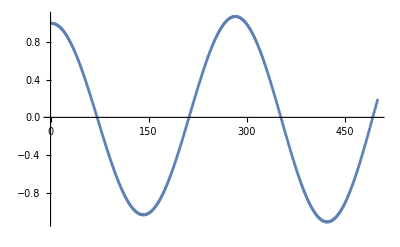

```mathematica
x0 = 1.0; (* Defines the initial position of the mass *) 

xdot0 = 0.0; (* Defines the initial velocity of the mass *) 

e = 0.01; (* Defines how much we increment by time *) 

xvalues= ConstantArray[0,500]; (* Defines an empty array of values for our position *) 

xdotvalues= ConstantArray[0,500]; (* Defines an empty array of values for our velocity *) 

xvalues[[1]] = x0; (* Sets first value of position array to the defined initial position *) 

xdotvalues[[1]] = xdot0; (* Sets first value of velocity array to the defined initial velocity *) 

For[i=2, (* Sets initial value of for loop *) 
i<501, (* Condition for for increment of for loop *) 
i++, (* Increment for loop by a single index *) 
xvalues[[i]] = xvalues[[i-1]]+e*xdotvalues[[i-1]]; (* Defines next x value as a first order Taylor series approximation of the position *) 
xdotvalues[[i]] = xdotvalues[[i-1]]-e*5.0*xvalues[[i-1]]] (* Defines next velocity value as a first order Taylor series approximation of the velocity *) 
ListPlot[xvalues] (* Plots the list of xvalues to yield a position as a function of time plot *)
```

```mathematica
(* Rewrite the code above so that it solves the differential equation for Pendulum Motion with initial conditions given in prompt *)

(* The only changes we make are to take
"x0 = Pi/2"
and "thetadotvalues[[i]] = thetadotvalues[[i-1]]-e*9.8*Sin[thetavalues[[i-1]]]"*)
```

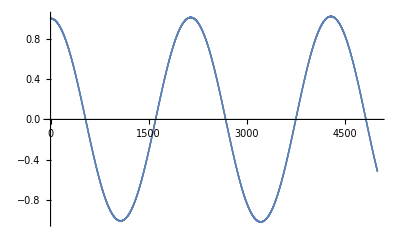

```mathematica
theta0 = Pi/2;

thetadot0 = 0.0;

e = 0.001;

thetavalues= ConstantArray[0,5000];

thetadotvalues= ConstantArray[0,5000];

thetavalues[[1]] = x0;

thetadotvalues[[1]] = xdot0;

For[i=2,
i<5001,
i++,
thetavalues[[i]] = thetavalues[[i-1]]+e*thetadotvalues[[i-1]];
thetadotvalues[[i]] = thetadotvalues[[i-1]]-e*9.8 *Sin[thetavalues[[i-1]]] ]

ListPlot[thetavalues]
```

```mathematica
(* If the length of the string is 1.0 meters and g = 9.8 meters/s^2, then the period of the pendulum (for the small-angle approximation) should be about 2.00 seconds. But the plot shows that we have a peak at about 2200*(0.01) = 2.2 seconds. This is consistent with our expectation that the small-angle approximation not be valid for theta = Pi/2 *)
```